```mathematica
firstFunction:=Sqrt[30]/(l^(5/2)) x (l-x)
```

```mathematica
anotherFunction:=132.816/(l^(9/2)) x(l-x) ((x-l/2)^2 - l^2/28)
```

```mathematica
triFunction:=c1 firstFunction + c2 anotherFunction
```

```mathematica
Integrate[ triFunction (-hbar^2/(2 m)   D[D[triFunction,x],x]),{x,0,l}]
```

(5. (1. c1^2+0.692822 c1 c2+10.2001 c2^2) hbar^2)/(l^2 m)

```mathematica
Integrate[triFunction triFunction,{x,0,l}]
```

0.+1. c1^2+1.00001 c2^2

```mathematica
eng:=Integrate[ triFunction (-hbar^2/(2 m)   D[D[triFunction,x],x]),{x,0,l}]/Integrate[triFunction triFunction,{x,0,l}]
```

```mathematica
eng
```

(5 (c1^2+0.692822 c1 c2+10.2001 c2^2) hbar^2)/((c1^2+c2^2) l^2 m)

```mathematica
Eigenvalues[{{5,0.6928220875962835 5},{0.6928220875962835 5,5 10.200051957551748}}]
```

{51.2597,4.74059}

```mathematica
Eigenvectors[{{5,0.6928220875962835 5},{0.6928220875962835 5,5 10.200051957551748}}]
```

{{0.074675,0.997208},{-0.997208,0.074675}}

```mathematica
(-hbar^2/(2 m)   D[D[firstFunction,x],x]- 4.740593435431725 firstFunction)/.{m->1,l->1,hbar->1}
```

√30-25.9653 (1-x) x

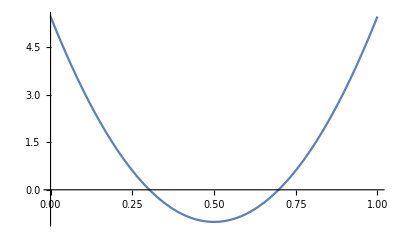

```mathematica
Plot[√30-25.96529960546866 (1-x) x,{x,0,1}]
```

```mathematica
(-hbar^2/(2 m)   D[D[anotherFunction,x],x]- .740593435431725` anotherFunction)/.{m->1,l->1,hbar->1}
```

-98.3627 (-1/28+(-1/2+x)^2) (1-x) x+1/2 (265.632 (-1/28+(-1/2+x)^2)-531.264 (1-x) (-1/2+x)-265.632 (1-x) x+531.264 (-1/2+x) x)

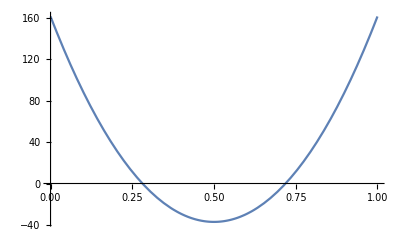

```mathematica
Plot[-98.36265772029998 (-1/28+(-1/2+x)^2) (1-x) x+1/2 (265.632 (-1/28+(-1/2+x)^2)-531.264 (1-x) (-1/2+x)-265.632 (1-x) x+531.264 (-1/2+x) x),{x,0,1}]
```